```mathematica
Graph[{1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11}, {Null, SparseArray[Automatic, {11, 11}, 0, {1, {{0, 5, 10, 14, 17, 22, 27, 33, 35, 40, 46, 50}, {{2}, {5}, {9}, {10}, {11}, {1}, {3}, {6}, {9}, {10}, {2}, {4}, {7}, {10}, {3}, {5}, {11}, {1}, {4}, {6}, {7}, {9}, {2}, {5}, {9}, {10}, {11}, {3}, {5}, {8}, {9}, {10}, {11}, {7}, {10}, {1}, {2}, {5}, {6}, {7}, {1}, {2}, {3}, {6}, {7}, {8}, {1}, {4}, {6}, {7}}}, Pattern}]}, {FormatType -> TraditionalForm, GraphLayout -> "CircularEmbedding"}]
```

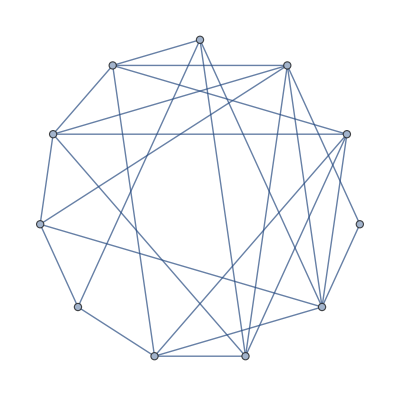
```mathematica
EdgeList[-Graphics-]
```

{1<->2,1<->5,1<->9,1<->10,1<->11,2<->3,2<->6,2<->9,2<->10,3<->4,3<->7,3<->10,4<->5,4<->11,5<->6,5<->7,5<->9,6<->9,6<->10,6<->11,7<->8,7<->9,7<->10,7<->11,8<->10}

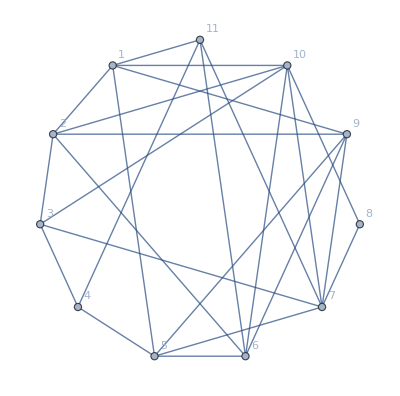

```mathematica
g=Graph[Range[10],{1<->2,1<->5,1<->9,1<->10,1<->11,2<->3,2<->6,2<->9,2<->10,3<->4,3<->7,3<->10,4<->5,4<->11,5<->6,5<->7,5<->9,6<->9,6<->10,6<->11,7<->8,7<->9,7<->10,7<->11,8<->10},VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

```mathematica
Select[FindFullFormula[g],SymbolLevel[#]==4&]
```

{v17x25bx368x49a,v17x258bx36x49a,v167x2x358bx49a,v167x2bx358x49a,v167x28x35bx49a,v167x28bx35x49a,v168x27x35bx49a,v16x27x358bx49a,v167x258bx3x49a,v167x258x3bx49a,v167x258x39bx4a,v167x258bx39x4a,v167x25bx389x4a,v167x25x389bx4a,v167x25x38bx49a,v167x25bx38x49a,v168x247x39x5ab,v168x247x39bx5a,v167x248x39x5ab,v167x248x39bx5a,v16x247x389x5ab,v16x247x389bx5a,v167x24x389x5ab,v167x24x389bx5a,v16x247x358x9ab,v168x247x35x9ab,v168x247x35bx9a,v16x247x358bx9a,v167x24x358x9ab,v167x248x35x9ab,v167x248x35bx9a,v167x24x358bx9a,v1467x2x389x5ab,v1467x2x389bx5a,v1467x2x358x9ab,v1467x2x358bx9a,v1467x2bx389x5a,v1467x2bx358x9a,v1467x28x39x5ab,v1467x28x39bx5a,v1467x28bx39x5a,v1467x28x35x9ab,v1467x28x35bx9a,v1467x28bx35x9a,v1468x27x39x5ab,v1468x27x39bx5a,v146x27x389x5ab,v146x27x389bx5a,v146x27x358x9ab,v146x27x358bx9a,v1468x27x35x9ab,v1468x27x35bx9a,v1467x258x3x9ab,v1467x258bx3x9a,v1467x258x3bx9a,v1467x258x39bxa,v1467x258x39xab,v1467x258bx39xa,v1467x25bx389xa,v1467x25x389xab,v1467x25x389bxa,v1467x25x38x9ab,v1467x25x38bx9a,v1467x25bx38x9a,v147x25x368x9ab,v147x25bx368x9a,v147x258x36x9ab,v147x258bx36x9a,v1368x27x49ax5b,v1368x27x49x5ab,v136x27x49ax58b,v136x27x489x5ab,v136x258bx49ax7,v1368x25bx49ax7,v138x25bx49ax67,v13x258bx49ax67,v136x258x47x9ab,v136x258bx47x9a,v1368x25x47x9ab,v1368x25bx47x9a,v13x258x467x9ab,v138x25x467x9ab,v138x25bx467x9a,v13x258bx467x9a,v1368x247x5x9ab,v1368x247x5bx9a,v136x247x5ax89b,v136x247x5abx89,v1368x247x5abx9,v1368x247x5ax9b,v136x247x58x9ab,v136x247x58bx9a}

```mathematica
Table[With[{g=MinimalGraph2[k]},Map[PartitionType[SymbolToSets[#]]&,Select[FindFullFormula[g],SymbolLevel[#]==4&]]],{k,3,12}]
```

{{{1,1,1,1}},{{2,1,1,1}},{{2,2,1,1}},{{2,2,2,1}},{{2,2,2,2}},{{3,3,2,1}},{{3,3,3,1}},{{4,3,2,2}},{{4,3,3,2}},{{4,4,3,2}}}

```mathematica
Table[With[{g=MinimalGraph2[k]},Select[FindFullFormula[g],SymbolLevel[#]==4&]],{k,13,14}]
```

{{v1dx25x379bex468ac},{v16bdx27acex359x48f}}

```mathematica
PartitionType[SymbolToSets[v1dx25x379bex468ac]]
```

{5,5,2,2}

```mathematica
PartitionType[SymbolToSets[v16bdx27acex359x48f]]
```

{5,4,3,3}

```mathematica
Monitor[Table[With[{g=MinimalGraph2[k]},Map[PartitionType[SymbolToSets[#]]&,Select[FindFullFormula[g],SymbolLevel[#]==4&]]],{k,3,15}],{"k",k}]
```